# 4. Sklop

## 1. naloga

```mathematica
p[x_]=x^4-3 x^3+a x^2+51x+b;
```

```mathematica
Solve[8 *2^x==16^(1/x),x]
```

{{x→-4},{x→1}}

```mathematica
Solve[p[-4]==0&&p[1]==0,{a,b}]
```

{{a→-13,b→-36}}

```mathematica
Solve[p[x]==0/.{a->-13,b->-36},x]
```

{{x→-4},{x→1},{x→3},{x→3}}

Odgovor : a=-13, b=-36,
                     ničle polinoma p so -4, 1, 3, 3.

## 2. naloga

### Naloga 2 a

```mathematica
p[x_]=x^2+2x-3;
q[x_]=x+1;
f[x_]=p[x]/q[x];
```

```mathematica
Solve[p[x]==0,x]
Solve[q[x]==0,x]
```

{{x→-3},{x→1}}

{{x→-1}}

```mathematica
PolynomialQuotient[p[x],q[x],x]
PolynomialRemainder[p[x],q[x],x]
```

1+x

-4

Odgovor : Ničli sta x=-3 in x=1,
                     pol je x=-1,
                     asimtota je y=x+1 ter ostanek je -4, zato graf ne seka asimptote.

### Naloga 2 b

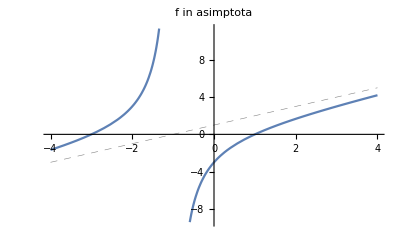

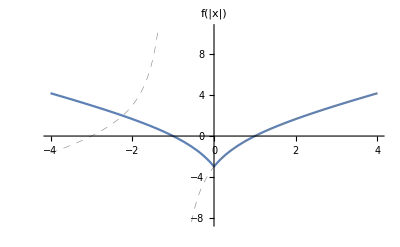

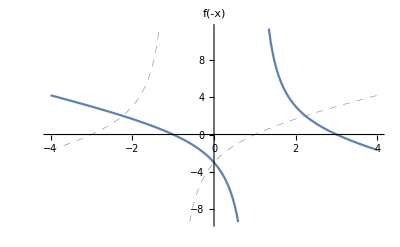

```mathematica
Plot[{f[x],x+1},{x,-4,4},PlotStyle->{Automatic,{Thickness[0.001], Dashed, Gray}},PlotLabel->"f in asimptota"]
Plot[{f[Abs[x]],f[x]},{x,-4,4},PlotStyle->{Automatic,{Thickness[0.001], Dashed, Gray}},PlotLabel->"f(|x|)"]
Plot[{f[-x],f[x]},{x,-4,4},PlotStyle->{Automatic,{Thickness[0.001], Dashed, Gray}},PlotLabel->"f(-x)"]
```

### Naloga 2 c

```mathematica
g[x_]=1/f[x];
h[x_]=q[x]/p[x];
```

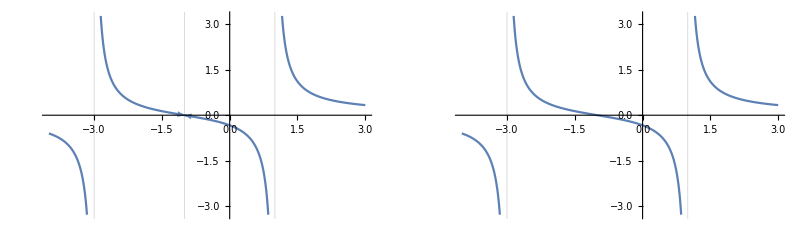

```mathematica
GraphicsRow[ {Plot[g[x],{x,-4,3},GridLines->{{-3,-1,1},{}},Epilog->{RGBColor[0.368417,0.506779,0.709798],Arrow[{{-1.1,h[-1.1]},{-1,h[-1]}}],Arrow[{{-0.9,h[-0.9]},{-1,h[-1]}}]}],
Plot[h[x],{x,-4,3},GridLines->{{-3,1},{}}]}]
```

Odgovor : Funkciji g in h nista enaki, saj se razlikujeta v definicijskem območju, velja namreč D_g=ℝ-{-3,-1,1} in D_h=ℝ-{-3,1}.

### Naloga 2 d

```mathematica
Solve[x==(3-x)/(x+1),x]
```

{{x→-3},{x→1}}

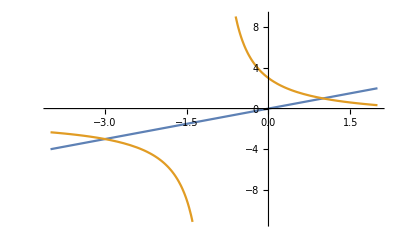

```mathematica
Plot[{x,(3-x)/(x+1)},{x,-4,2}]
```

Odgovor : x∈[-3,-1)∪[1,∞)

## 3. naloga

### Naloga 3 a

```mathematica
p[x_]=2 x^4-x^3-9 x^2+4x+4;
q[x_]=x^2+x;
f[x_]=p[x]/q[x];
```

```mathematica
Solve[p[x]==0,x]
Solve[q[x]==0,x]
```

{{x→-2},{x→-1/2},{x→1},{x→2}}

{{x→-1},{x→0}}

```mathematica
PolynomialQuotient[p[x],q[x],x]
PolynomialRemainder[p[x],q[x],x]
```

-6-3 x+2 x^2

4+10 x

```mathematica
Solve[4+10 x==0,x]
```

{{x→-2/5}}

Odgovor : Ničle so x=-2, x=-1/2, x=1 in x=2,
                     pola sta x=-1 in x=0,
                     asimtota je y=2 x^2-3x-6 ter ostanek je 10x+4, zato graf seka asimptoto pri x=-2/5.

### Naloga 3 b

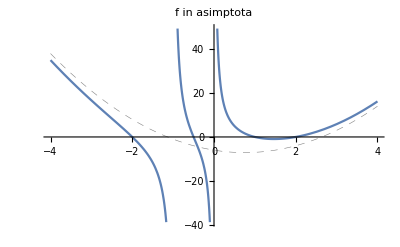

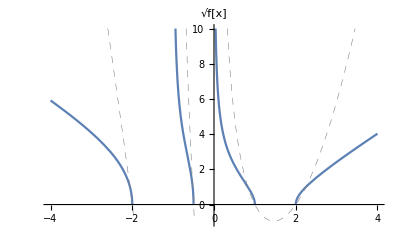

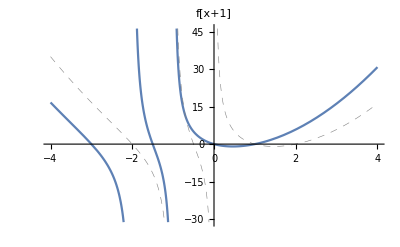

```mathematica
Plot[{f[x],-6-3 x+2 x^2},{x,-4,4},PlotStyle->{Automatic,{Thickness[0.001], Dashed, Gray}},PlotLabel->"f in asimptota"]
Plot[{√f[x],f[x]},{x,-4,4},PlotStyle->{Automatic,{Thickness[0.001], Dashed, Gray}},PlotRange->{-1,10},PlotLabel->"√f[x]"]
Plot[{f[x+1],f[x]},{x,-4,4},PlotStyle->{Automatic,{Thickness[0.001], Dashed, Gray}},PlotLabel->"f[x+1]"]
```

### Naloga 3 c

Odgovor : x∈(-2,-1)∪(-1/2,0)∪(1,2)

## 4. naloga

```mathematica
p[x_]=α(x+2)(x+1)(x-1);
q[x_]=x^2+β x+γ;
```

```mathematica
PolynomialQuotient[p[x],q[x],x]
```

2 α+x α-α β

```mathematica
Solve[α==1&&2 α-α β==2,{α,β}]
```

{{α→1,β→0}}

```mathematica
Solve[p[0]/q[0]==-2/.{α->1,β->0},γ]
```

{{γ→1}}

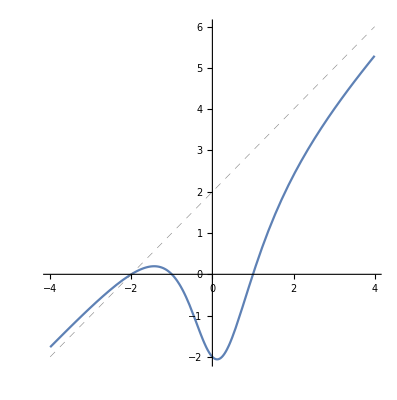

```mathematica
Plot[{p[x]/q[x]/.{α->1,β->0,γ->1},x+2},{x,-4,4},PlotStyle->{Automatic,{Thickness[0.001], Dashed,Gray}},AspectRatio->Automatic]
```